# Doppler Effect Simulation

Yousef Sadeghi
Department of Physics, Faculty of Science, Ferdowsi University of Mashhad
Arash T. Jamshidi
Department of Physics, Faculty of Science, Ferdowsi University of Mashhad

I.  INTRODUCTION

The Doppler effect is the change in frequency of a wave in relation to an observer who is moving relative to the wave source. It is named after the Austrian physicist Christian Doppler, who described the phenomenon in 1842. A common example of Doppler effect is the change of pitch heard when a vehicle sounding a horn approaches and recedes from an observer. Compared to the emitted frequency, the received frequency is higher during the approach, identical at the instant of passing by, and lower during the recession.
The reason for the Doppler effect is that when the source of the waves is moving towards the observer, each successive wave crest is emitted from a position closer to the observer than the crest of the previous wave. Therefore, each wave takes slightly less time to reach the observer than the previous wave. Hence, the time between the arrivals of successive wave crests at the observer is reduced, causing an increase in the frequency.

II.  Stationary Source
The program produces multiple circles with the same center and the radius of each circle is determined by variable ν so that radius difference between two consecutive circles is ν units, Circles visualize wave crests.

```mathematica
λ:=5
(*scale*)
g:=Graphics[{AbsolutePointSize[5],Point[{0,0}]}]
(*source*)
n:=1
(*number of waves - 1*)
w01[r_]:=Table[If[(r-i*λ)≥ 0,ContourPlot[x^2+y^2==(r-i*λ)^2,{x,-(n+1)*λ,(n+1)*λ},{y,-(n+1)*λ,(n+1)*λ},PlotTheme->"Scientific",PlotRange->{{-(n+1)*λ,(n+1)*λ},{-(n+1)*λ,(n+1)*λ}}],g],{i,0,n}]
(*waves*)
Manipulate[Show[w01[r],g],{r,10^-100,(n+1)*λ}]
```

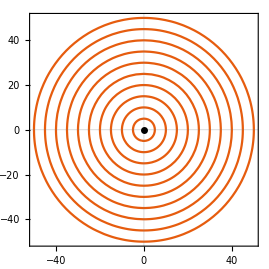
-Graphics-
Stationary sound source produces sound waves at a constant frequency, and the wave-fronts propagate symmetrically away from the source at a constant speed. All observers will hear the same frequency, which will be equal to the actual frequency of the source.

III.  Moving Source

A.  Two-Dimensional Space
The program produces multiple circles with different coordinates which shows us movement of the source, variables “vx” and “vy” determine velocity of  the source respectively in x-direction and y-direction. Circles visualize wave crests which Expand at rate of  “cs” that represents speed of sound.

```mathematica
vx:=1
(*velocity in the x direction*)
vy:=0
(*velocity in the y direction*)
cs:=1
(*speed of wave / scale*)
p01:=Plot[0,{x,0,0.0001}]
(*just a point to force if command work*)
s2d[r_]:=Graphics[{AbsolutePointSize[5],Black,Point[{(vx*r)/cs,(vy*r)/cs}]}]
(*source*)
n:=10
(*number of waves*)
w02[Xv_,Yv_,r_]:=Table[If[(r-i*cs)≥ 0,ContourPlot[(x-i*Xv)^2+(y-i*Yv)^2==(r-i*cs)^2,{x,-(n+1)*cs,(n+1)*cs},{y,-(n+1)*cs,(n+1)*cs},PlotTheme->"Scientific",PlotRange->{{-(n+1)*cs,(n+1)*cs},{-(n+1)*cs,(n+1)*cs}}],p01],{i,0,n}]
(*waves*)
Manipulate[Show[w02[vx,vy,r],s2d[r]],{r,10^-100,(n+1)*cs}]
```

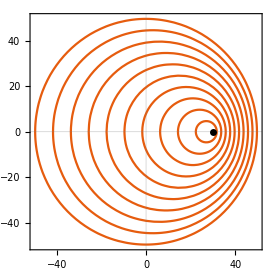
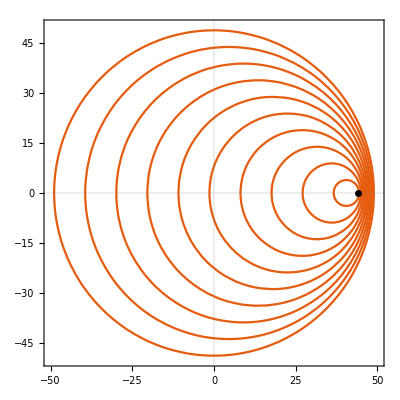
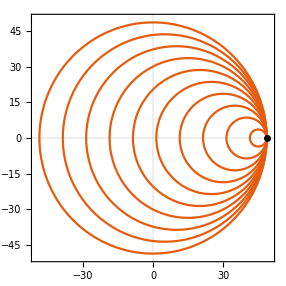
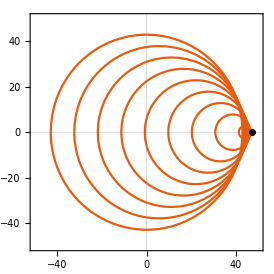
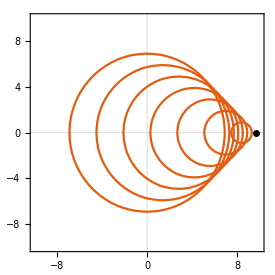
-Graphics--Graphics-
vx < cs
The same sound source is radiating sound waves at a constant frequency. Since the source is moving, the center of each new wave front is now slightly displaced to the right. As a result, the wave-fronts begin to bunch up on the right side (in front of) and spread further apart on the left side (behind) of the source. An observer in front of the source will hear a higher frequency and an observer behind the source will hear a lower frequency.

-Graphics-
vx = cs
Now the source is moving at the speed of sound. The wave fronts in front of the source are now all bunched up at the same point. As a result, an observer in front of the source will detect nothing until the source arrives and an observer behind the source will hear a lower frequency.
      
-Graphics--Graphics-
vx > cs
The sound source has now surpassed the speed of sound. Since the source is moving faster than the sound waves it creates, it actually leads the advancing wave front(mach cone). The sound source will pass by a stationary observer before the observer hears the sound.

B.  Three-Dimensional Space
The program produces multiple spheres with different coordinates which shows us movement of the source, variables “vx”, “vy” and “vz” determine velocity of  the source respectively in x-direction, y-direction and z-direction. Spheres visualize wave crests which Expand at rate of  “cs” that represents speed of sound.

```mathematica
vx:=5
(*velocity in the x direction*)
vy:=5
(*velocity in the y direction*)
vz:=5
(*velocity in the z direction*)
cs:=5
(*speed of wave / scale*)
w02[Xv_,Yv_,Zv_,r_]:=Table[If[(r-i*cs)≥ 0,ContourPlot3D[(x-i*Xv)^2+(y-i*Yv)^2+(z-i*Zv)^2==(r-i*cs)^2,{x,-(n+1)*cs,(n+1)*cs},{y,-(n+1)*cs,(n+1)*cs},{z,-10*cs,10*cs},PlotTheme->"Scientific",PlotRange->{{-(n+1)*cs,(n+1)*cs},{-(n+1)*cs,(n+1)*cs},{-(n+1)*cs,(n+1)*cs}},Mesh->None,ContourStyle->Opacity[0.1],PlotPoints->25],p02],{i,0,n}]
(*waves*)
p02:=Plot3D[0,{x,0,0.000001},{y,0,0.000001}]
(*just a point (doesn't matter)*)
s3d[r_]:=Graphics3D[{AbsolutePointSize[5],Point[{(vx*r)/cs,(vy*r)/cs,(vz*r)/cs}]}]
(*source*)
n:=10
(*number of waves*)
Manipulate[Show[w02[vx,vy,vz,r],s3d[r]],{r,10^-100,(n+1)*cs}]
```